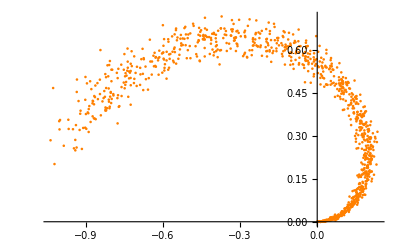

```mathematica
manifold=Table[AngleVector[{x,0.9 Pi x}]+x/20*RandomVariate[NormalDistribution[],2],{x,0,1,0.001}];
plot=ListPlot[manifold,PlotStyle->Orange]
```

```mathematica
net=NetChain[{25,Ramp,1,25,Ramp,2},"Input"->2]
```

NetChain[]

```mathematica
lossNet=NetGraph[{net,MeanSquaredLossLayer[]},{1->2,NetPort["Input"]->NetPort[2,"Target"]}]
```

NetGraph[]

```mathematica
lossNet=NetTrain[lossNet,<|"Input"->manifold|>,BatchSize->4096];
trained=NetExtract[lossNet,1];
```

NetChain::invindata2: Data supplied to port "Input" was not a length-2 vector.

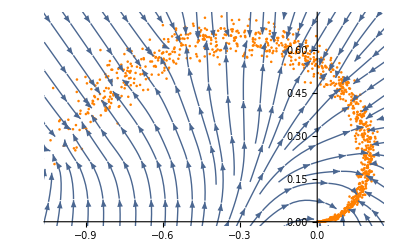

```mathematica
{{xmin,xmax},{ymin,ymax}}=CoordinateBounds[manifold,.2];
Show[plot,StreamPlot[trained[{x,y}]-{x,y},{x,xmin,xmax},{y,ymin,ymax}]]
```

```mathematica
decoder=Drop[trained,3]
encoder=Take[trained,3]
```

NetChain[]

NetChain[]

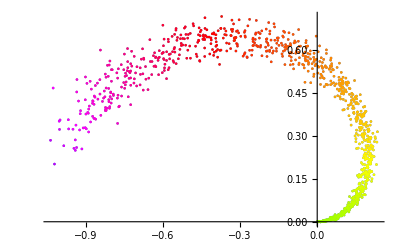

```mathematica
ListPlot[Style[#,Hue[First[0.3+encoder[#]]/3]]&/@manifold]
```

```mathematica
{min,max}=MinMax[encoder[manifold]]
```

{-0.934625,0.404101}

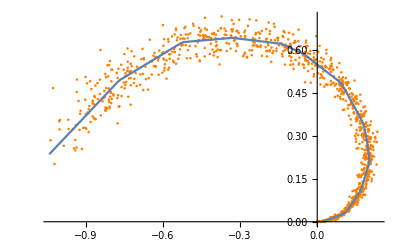

```mathematica
Show[plot,ListLinePlot[Table[decoder[x],{x,min,max,.01}]]]
```

```mathematica
net1=NetChain[{ElementwiseLayer[Ramp],SummationLayer[]}]
```

NetChain[]

```mathematica
net1[{-2,-1,0,1,2.5}]
```

3.5